This notebook generates Local Chern Number of the BHZ model (Quantum Anomalous Hall Insulator (QAHI)) on a projected brane. Then it gathers the local Chern number of the sites on the middle line of the brane, and exports them to a .dat file

The .dat files generated with this notebook can be visualized with Make_Plots_Local_Chern_Number_projected_Brane.nb

```mathematica
tStart=AbsoluteTime[];
```

```mathematica
Clear[Lx,Ly,A,
sx2d,SX2D,sx2dp,SX2DP,
sy2d,SY2D,sy2dp,SY2DP,
cx2d,CX2D,cx2dp,CX2DP,
cy2d,CY2D,cy2dp,CY2DP,
cons,Cons]
```

```mathematica
(** Change Lx, Ly and m in the following lines before running the code **)
```

```mathematica
(** we will set t = 2 t0 = 1. **)
```

```mathematica
t=1;
t0 = 0.5;
m =  6 * t0;
```

```mathematica
L=100;
```

```mathematica
Lx=L;
Ly=L;
A=Lx*Ly;
```

```mathematica
(**-----------------Define the sine and cosine matrices for the parent square lattice--------------------**)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx2d[i_Integer,j_Integer]=0;

Do[Do[{sx2d[j+k Lx,j+1+k Lx]=-I/2,sx2d[j+1+k Lx,j+k Lx]=I/2},{j,1,Lx-1}],{k,0,Ly-1}]

SX2D=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sx2dp[i_Integer,j_Integer]=0;

Do[{sx2dp[(k+1)Lx,1+k Lx]=-I/2,sx2dp[1+k Lx,(k+1)Lx]=I/2},{k,0,Ly-1}]

SX2DP=Table[sx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy2d[i_Integer,j_Integer]=0;

Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2,sy2d[(k+1)Lx+j,k Lx+j]=I/2},{j,1,Lx}],{k,0,Ly-2}]

SY2D=Table[sy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy2dp[i_Integer,j_Integer]=0;

Do[{sy2dp[(Ly-1)Lx+j,j]=-I/2,sy2dp[j,(Ly-1)Lx+j]=I/2},{j,1,Lx}]

SY2DP=Table[sy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx2d[i_Integer,j_Integer]=0;

Do[Do[{cx2d[j+k Lx,j+1+k Lx]=1/2,cx2d[j+1+k Lx,j+k Lx]=1/2},{j,1,Lx-1}],{k,0,Ly-1}]

CX2D=Table[cx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cx2dp[i_Integer,j_Integer]=0;

Do[{cx2dp[(1+k)Lx,1+k Lx]=1/2,cx2dp[1+k Lx,(1+k)Lx]=1/2},{k,0,Ly-1}]

CX2DP=Table[cx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy2d[i_Integer,j_Integer]=0;

Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2,cy2d[(k+1)Lx+j,k Lx+j]=1/2},{j,1,Lx}],{k,0,Ly-2}]

CY2D=Table[cy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy2dp[i_Integer,j_Integer]=0;

Do[{cy2dp[(Ly-1)Lx+j,j]=1/2,cy2dp[j,(Ly-1)Lx+j]=1/2},{j,1,Lx}]

CY2DP=Table[cy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix for the parent square lattice---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianQAHI]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
(** Define the Hamiltonian **)
```

```mathematica
(** PBC is α = 1, OBC is α = 0 **)
```

```mathematica
HamiltonianQAHI[t_,t0_,m_,α_]:=t*(KroneckerProduct[SX2D+α*SX2DP,σ1]+KroneckerProduct[SY2D+α*SY2DP, σ2])-KroneckerProduct[m*Cons-2t0*(2 * Cons -CX2D-CY2D-α*CX2DP-α*CY2DP),σ3]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------------Projected Brane--------------------------*)
```

```mathematica
Clear[Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
NOrbitals=Dimensions[FlatSite][[1]]
```

800

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals,2}];
```

```mathematica
(**--Equations for the two red lines--**)
```

```mathematica
(** Comment/Uncomment the rational and irrational equations accordingly **)
```

```mathematica
(**-------Irrational-------**)
```

```mathematica
LineUp[x_]:=((1+√5)/2)^-1*(x-1)+22
LineDn[x_]:=((1+√5)/2)^-1*(x-2)+12
```

```mathematica
(**-------Rational-------**)
```

```mathematica
(** LineUp[x_]:=(2/3)(x-1)+22
LineDn[x_]:=(2/3)*(x-2)+12 **)
```

```mathematica
(** We make a plot of the projected brane, for the purpose of illustration **)
```

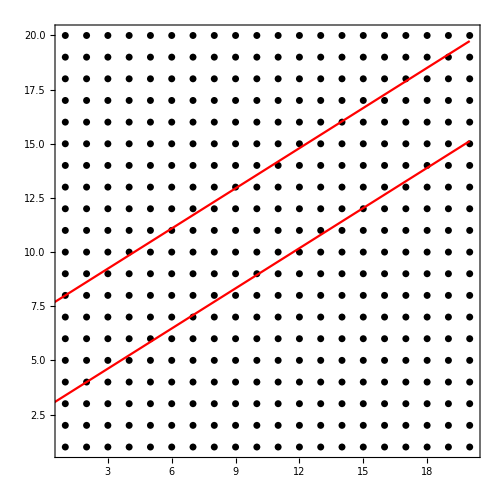

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
Plot[LineUp[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineDn[x],{x,0,Lx},PlotStyle-> Red],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
ImageSize-> 500,AspectRatio-> 1
]
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[Fibonup,Fibondown,TotalFibon,XList, YList, XListKron, YListKron]
```

```mathematica
(**-----We want to isolate points inside the projected brane (between the red lines), store them in FibonupNew, and sort them into Fibonup-----**)
```

```mathematica
Clear[FibonupNew]
FibonupNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
Do[Do[FibonupNew=Append[FibonupNew,x+(y-1)*Lx],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx}]
```

```mathematica
(** Site indices of the sites in the projected brane **)
```

```mathematica
Fibonlist=Sort[FibonupNew];
```

```mathematica
(** List of Y coordinates of the sites in the projected brane **)
```

```mathematica
YList = Ceiling[Fibonlist/Lx];
```

```mathematica
(** List of X coordinates of the sites in the projected brane **)
```

```mathematica
XList = Fibonlist - (YList - 1)Lx;
```

```mathematica
(** Repeat the coordinates for the two onsite orbitals **)
```

```mathematica
XListKron = Flatten[KroneckerProduct[XList,{1,1}],2];
```

```mathematica
YListKron = Flatten[KroneckerProduct[YList,{1,1}],2];
```

```mathematica
(**----Generate indices for the two orbitals, and group them into TotalFibon----**)
```

```mathematica
Fibonup = 2 * Fibonlist -1;
```

```mathematica
Fibondown = 2 * Fibonlist;
```

```mathematica
TotalFibon=Flatten[{Fibonup,Fibondown}];
```

```mathematica
(** This list contains (original) indices of the orbitals within the projected brane **)
```

```mathematica
TotalFibon = Sort[TotalFibon];
```

```mathematica
NOrbitalsBrane=Dimensions[TotalFibon][[1]]
```

182

```mathematica
NOrbitalsBrane/2
```

91

```mathematica
NOrbitalsOutside = NOrbitals-NOrbitalsBrane
```

618

```mathematica
(** Percentage of sites within the Brane **)
```

```mathematica
Percentage = N[NOrbitalsBrane/(2*A)]
```

0.2275

```mathematica
(*-------------F1 is the list of all orbitals in the parent lattice. a is the list of orbitals outside the brane -----------------*)
```

```mathematica
Clear[F1,a]
```

```mathematica
F1=Table[i,{i,1,2*A}];
```

```mathematica
Dimensions[F1]
```

{800}

```mathematica
a= Complement[F1, TotalFibon];
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*----------------------------Create matrices for the Hamiltonian of the projected brane-------------------------------------------*)
```

```mathematica
Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D]
```

```mathematica
(** We first generate the Hamiltonian on the square lattice, with t = t0 = 1, under Open Boundary Conditions **)
```

```mathematica
HTrial=HamiltonianQAHI[t,t0,m,0.0];
```

```mathematica
Clear[sx2d,sx2dp,cx2d,cx2dp,sy2d,sy2dp,cy2d,cy2dp,SX2D,SX2DP,CX2D,CX2DP,SY2D,SY2DP,CY2D,CY2DP,Cons,cons]
```

```mathematica
(*---------------This is H11-----------------*)
```

```mathematica
Hfbfb[i_Integer,j_Integer]=0;
Do[
Do[
Hfbfb[i,j]=HTrial[[TotalFibon[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsBrane}
],
{j,1,NOrbitalsBrane}
]
HFBFB=Table[Hfbfb[i,j],{i,1,NOrbitalsBrane},{j,1,NOrbitalsBrane}];
```

```mathematica
(*--------------------This is H22-----------------*)
```

```mathematica
H2d2d[i_Integer,j_Integer]=0;
Do[
Do[
H2d2d[i,j]=HTrial[[a[[i]],a[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsOutside}
]
H2D2D=Table[H2d2d[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsOutside}];
```

```mathematica
(*------------------This is H21------------------*)
```

```mathematica
H2dfb[i_Integer,j_Integer]=0;

Do[
Do[
H2dfb[i,j]=HTrial[[a[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsBrane}
]
H2DFB=Table[H2dfb[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsBrane}];
```

```mathematica
(*------------------This is H12------------------*)
```

```mathematica
Hfb2d[i_Integer,j_Integer]=0;

Do[
Do[
Hfb2d[i,j]=HTrial[[TotalFibon[[i]],a[[j]]]],
{i,1,NOrbitalsBrane}
],
{j,1,NOrbitalsOutside}
]
HFB2D=Table[Hfb2d[i,j],{i,1,NOrbitalsBrane},{j,1,NOrbitalsOutside}];
```

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[HFibonRenor,ValueFibon,VecFibon,ValVecFibon,ValFibon]
```

```mathematica
(** This is the effective Hamiltonian HPTB, defined in Eq. 1 in our paper **)
```

```mathematica
HFibonRenor=HFBFB-(HFB2D.Inverse[H2D2D].H2DFB);
```

```mathematica
(** To save memory, I delete some matrices which I no longer need **)
```

```mathematica
Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D]
```

```mathematica
(**------Check that HFibonRenor is Hermitian------**)
```

```mathematica
(**--- ConjugateTranspose[HFibonRenor] - HFibonRenor//Chop ---**)
```

```mathematica
(** --------------------------------------------------------- **)
```

```mathematica
(**-----------Diagonalize HPTB----------------**)
```

```mathematica
{ValueFibon,VecFibon}=Eigensystem[HFibonRenor];
```

```mathematica
ValVecFibon=SortBy[Transpose[{ValueFibon,VecFibon}],First];
```

```mathematica
ValFibon=Table[{j,ValVecFibon[[j,1]]},{j,1,NOrbitalsBrane}]//Chop;
```

```mathematica
(**------------------- Real space Chern number calculation as per PHYSICAL REVIEW B 84,241106(R) (2011) -------------------**)
```

```mathematica
FilledEigenvectors=Table[ValVecFibon[[i]][[2]], {i,1,NOrbitalsBrane/2}];
```

```mathematica
Clear[P,Q,ChernMatrix,ChernMatrixDiagonalList,ChernMatrixSiteWiseList]
```

```mathematica
(** We create a projector P on the space of filled eigenstates (half-filling limit) **)
```

```mathematica
P = Table[0,{i,1,NOrbitalsBrane},{j,1,NOrbitalsBrane}];
```

```mathematica
Do[P+=TensorProduct[FilledEigenvectors[[i]] ,Conjugate[ FilledEigenvectors[[i]]]],{i, 1, NOrbitalsBrane/2}];
```

```mathematica
Dimensions[P]
```

{182,182}

```mathematica
Q =  IdentityMatrix[NOrbitalsBrane] - P;
```

```mathematica
percentageOfOrbitalsInside = N[NOrbitalsBrane/(2*A)]
```

0.2275

```mathematica
NSitesInside = NOrbitalsBrane/2
```

91

```mathematica
X1 = DiagonalMatrix[XListKron];
```

```mathematica
Y1 = DiagonalMatrix[YListKron];
```

```mathematica
Max[Abs[P.Q]]
```

1.44158×10^-14

```mathematica
(** Define the local Chern operator **)
```

```mathematica
ChernMatrix=-4π Im[(P.X1.Q.Y1.P)];
```

```mathematica
(** This is the Wanneir orbitalwise list **)
```

```mathematica
ChernMatrixDiagonalList= Diagonal[ChernMatrix];
```

```mathematica
(** Here I take two elements of the list at a time to add the contribution of both onsite orbitals **)
```

```mathematica
ChernMatrixSiteWiseList = Table[ChernMatrixDiagonalList[[2 i]]+ChernMatrixDiagonalList[[2i-1]],{i,1,NOrbitalsBrane/2}];
```

```mathematica
(**------------------------String manipulations for exporting the local Chern values in a dat file------------------------**)
```

```mathematica
Clear[location,filename1,filename2,filenameString1,filenameString2,filenameString3,filenameString4,filenameString5,filenameString6]
```

```mathematica
location="dataPTB/";
```

```mathematica
filenameString1 = "dataPTBlocalChernAllSitesLx=";
filenameString1a = "dataPTBlocalChernSitesOnLineLx=";
filenameString2="Ly=";
filenameString3 = "mbyt0=";
filenameString4 = "Xup=";
filenameString5 = "Xdn=";
percentageString = "PartsPerThousand=";
```

```mathematica
(** This part checks whether the slope is rational/irrational, to make the filename **)
```

```mathematica
slope = D[LineUp[x],x];
If[Element[slope,Rationals]==True,filenameString6="Rational",filenameString6="Irrational"];
```

```mathematica
(** Finally, we create the filename. The filenames contain infomation about Lx, Ly, Xup, Xdn, the fraction of sites within the projected Brane, and whether the lines defining the brane are rational or irrational. **)
```

```mathematica
filename1 = StringJoin[location,filenameString1,ToString[Lx],filenameString2,ToString[Ly],filenameString3,ToString[m],filenameString4,ToString[LineUp[1]],filenameString5,ToString[LineDn[2]],percentageString,ToString[Round[percentageOfOrbitalsInside * 1000]],filenameString6,".dat"]
```

```mathematica
filename2 = StringJoin[location,filenameString1a,ToString[Lx],filenameString2,ToString[Ly],filenameString3,ToString[m],filenameString4,ToString[LineUp[1]],filenameString5,ToString[LineDn[2]],percentageString,ToString[Round[percentageOfOrbitalsInside * 1000]],filenameString6,".dat"]
```

```mathematica
(** This contains {SiteIndexInOriginalCrystal,Chern(x,y)} **)
```

```mathematica
SiteIndexLocalChern=Table[{XList[[ii]]+(YList[[ii]]-1)*Lx,ChernMatrixSiteWiseList[[ii]]},{ii,1,NOrbitalsBrane/2}];
```

```mathematica
(** This contains {x,y,LocalChern(x,y)} **)
```

```mathematica
SiteCoordinateLocalChern=Table[{XList[[ii]],YList[[ii]],ChernMatrixSiteWiseList[[ii]]},{ii,1,NOrbitalsBrane/2}];
```

```mathematica
(** Equation of the middle line (green) **)
```

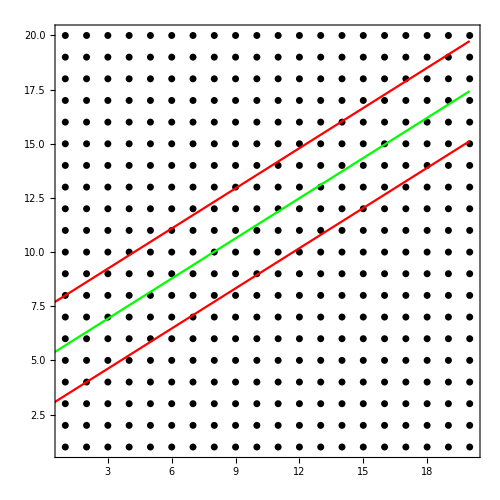

```mathematica
LineMid[x_]:=(LineDn[x]+LineUp[x])/2;
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
Plot[LineUp[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineDn[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineMid[x],{x,0,Lx},PlotStyle-> Green],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
ImageSize-> 500,AspectRatio-> 1
]
```

```mathematica
(** Sites closest to the middle line **)
```

```mathematica
NearestSiteCoordinateList=Table[{x,Round[LineMid[x]]},{x,1,Lx}]
```

{{1,6},{2,6},{3,7},{4,8},{5,8},{6,9},{7,9},{8,10},{9,11},{10,11},{11,12},{12,12},{13,13},{14,14},{15,14},{16,15},{17,16},{18,16},{19,17},{20,17}}

```mathematica
Fibonlist;
```

```mathematica
(** Indices within Fibonlist of the sites in the middle line**)
```

```mathematica
WhichIndicesInFibonlistAreOnTheMiddleLine=Table[Flatten[Position[Fibonlist,NearestSiteCoordinateList[[ii]][[1]] +(NearestSiteCoordinateList[[ii]][[2]]-1)*Lx ]] [[1]],{ii,1,Lx}]
```

{5,6,12,18,19,26,27,34,41,42,49,50,56,63,64,71,78,79,85,86}

```mathematica
(** Here we collect the local Chern number values on the points closest to the middle line **)
```

```mathematica
LineChernList = Table[ChernMatrixSiteWiseList[[WhichIndicesInFibonlistAreOnTheMiddleLine[[ii]]]],{ii,1,Lx}]
```

{-4.68185,0.873571,0.230891,0.925252,0.897871,0.965739,0.950629,0.959162,0.95469,0.966834,0.966873,0.951583,0.965995,0.942,0.939853,0.892453,0.819857,0.483878,0.796448,-3.90453}

```mathematica
LineChernListExport = Table[{NearestSiteCoordinateList[[ii]][[1]],NearestSiteCoordinateList[[ii]][[2]],LineChernList[[ii]]},{ii,1,Lx}]
```

{{1,6,-4.68185},{2,6,0.873571},{3,7,0.230891},{4,8,0.925252},{5,8,0.897871},{6,9,0.965739},{7,9,0.950629},{8,10,0.959162},{9,11,0.95469},{10,11,0.966834},{11,12,0.966873},{12,12,0.951583},{13,13,0.965995},{14,14,0.942},{15,14,0.939853},{16,15,0.892453},{17,16,0.819857},{18,16,0.483878},{19,17,0.796448},{20,17,-3.90453}}

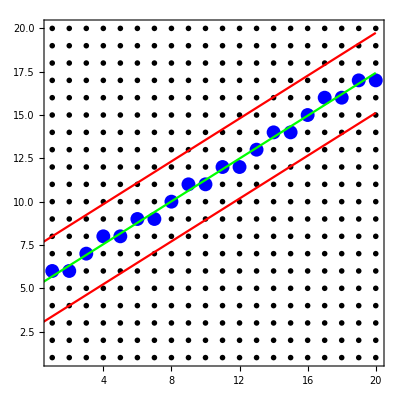

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
ListPlot[NearestSiteCoordinateList,PlotStyle-> {Blue,PointSize[0.025]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
Plot[LineUp[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineDn[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineMid[x],{x,0,Lx},PlotStyle-> Green],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 18,
ImageSize-> 400,AspectRatio-> 1
]
```

```mathematica
(** Here we export the files **)
```

```mathematica
(** This file contains all the local Chern values on the PTB **)
```

```mathematica
Export[filename1,SiteCoordinateLocalChern];
```

```mathematica
(** This file contains the local Chern values middle line on the PTB **)
```

```mathematica
Export[filename2,LineChernListExport];
```

```mathematica
(**----------------------------------------------------------------------------------------**)
```

```mathematica
(**-------------------Here we generate a Histogram for the purpose of illustration, but the plots are created with Make_Plots_Local_Chern_Number_projected_Brane.nb------------------------**)
```

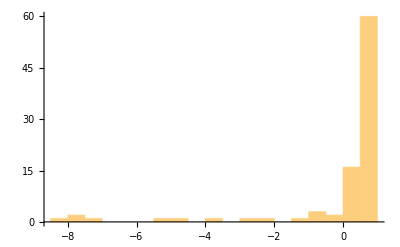

```mathematica
Histogram[ChernMatrixSiteWiseList]
```

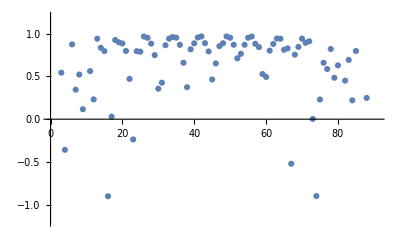

```mathematica
ListPlot[ChernMatrixSiteWiseList,PlotRange->{-1.2,1.2}]
```

```mathematica
Mean[ChernMatrixSiteWiseList]
```

9.565×10^-16

```mathematica
tStop=AbsoluteTime[];
```

```mathematica
tStop - tStart
```

57.081936